## Initializing all variables

### Loading

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
polarorder=Import["data/globalpolarorders.mx"];
nematicorder=Import["data/globalnematicorders.mx"];
totfractpolorder=Import["data/localpolarorders.mx"];
totfractnemorder=Import["data/localnematicorders.mx"];
```

```mathematica
{ensemblesize,snapcount2}= Dimensions@polarorder
```

{20,1001}

```mathematica
tmax=60000.;
timegrid2=Range[0,tmax,tmax/(snapcount2-1)];
```

## Order parameters

### Global nematic order

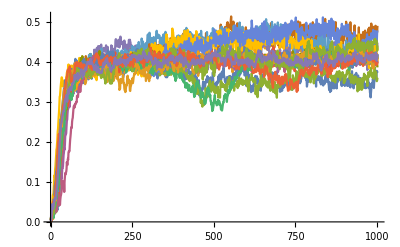

```mathematica
ListLinePlot[nematicorder,PlotRange->All]
```

### Global polar order

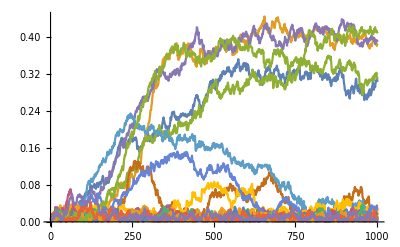

```mathematica
ListLinePlot[polarorder,PlotRange->All]
```

### All order parameters, individual traces

```mathematica
Manipulate[ListPlot[{polarorder[[i]],nematicorder[[i]],totfractpolorder[[i]],totfractnemorder[[i]]},Joined->True],{i,1,ensemblesize,1}]
```

### Local polar order

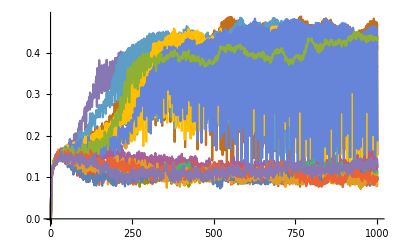

```mathematica
ListPlot[totfractpolorder,Joined->True]
```

## Fitting

note that all time units are not normalized up to the factor L/v=6.3

### polar fixation times

```mathematica
interval=50;
smopol=Table[MovingAverage[totfractpolorder[[idx]],interval],{idx,1,ensemblesize}];
smonem=Table[MovingAverage[totfractnemorder[[idx]],interval],{idx,1,ensemblesize}];
polvar=Table[Table[Sqrt@Variance[totfractpolorder[[idx,t;;t+interval-1]]],{t,1,snapcount2-interval+1}],{idx,1,ensemblesize}];
nemvar=Table[Table[Sqrt@Variance[totfractnemorder[[idx,t;;t+interval-1]]],{t,1,snapcount2-interval+1}],{idx,1,ensemblesize}];
```

```mathematica
deltaorder=smopol+polvar-(smonem-nemvar);
switchindices=Table[(Position[Differences@Sign[deltaorder[[idx]]],n_/;n!=0]+1),{idx,1,ensemblesize}];
switchtimes=Table[Flatten@(timegrid2[[#]]&/@switchindices[[idx]])+Mean@timegrid2[[;;interval]],{idx,1,ensemblesize}];
```

```mathematica
testcase=Table[0<#&/@deltaorder[[idx,-10;;]],{idx,1,ensemblesize}];
patternstate=Table[Switch[Length@Cases[testcase[[idx]],True],Length@testcase[[idx]],"polar",0,"nematic",_,"inconclusive"],{idx,1,ensemblesize}]
```

{polar,polar,polar,nematic,polar,polar,polar,polar,nematic,nematic,nematic,polar,nematic,nematic,nematic,nematic,nematic,polar,nematic,nematic}

```mathematica
polarfixationtime=Flatten[{#,switchtimes[[#,2]]}]&/@Position[patternstate,"polar"]
(*nematicfixationtime=Flatten[{#,switchtimes[[#,1]]}]&/@Position[patternstate,"nematic"]
fixationtimes=SortBy[Flatten[{polarfixationtime,nematicfixationtime},1],First]*)
```

{{1,24630.},{2,17310.},{3,25590.},{5,6570.},{6,12510.},{7,10770.},{8,14250.},{12,16890.},{18,12630.}}

### fitting and nematic fixation times

```mathematica
localpolfit=Table[NonlinearModelFit[Thread[{timegrid2,totfractpolorder[[idx]]}],Piecewise[{{a time, time<burntime},{a burntime-c (time-burntime)^2,burntime<=time<consttime},{a burntime- c (consttime-burntime)^2,time≥consttime}}],{a,{burntime,1000},c,{consttime,8000}},time],{idx,1,ensemblesize}];
```

```mathematica
localnemfit=Table[NonlinearModelFit[Thread[{timegrid2,totfractnemorder[[idx]]}],Piecewise[{{a time, time<burntime},{a burntime-c (time-burntime),burntime<=time<consttime},{a burntime- c (consttime-burntime),time≥consttime}}] ,{a,{burntime,1000},c,{consttime,8000}},time],{idx,1,ensemblesize}];
```

```mathematica
localordertime=Flatten@Table[Mean[burntime/.#&/@{localpolfit[[idx]][{"BestFitParameters"}],localpolfit[[idx]][{"BestFitParameters"}]}],{idx,1,ensemblesize}];
```

```mathematica
nematicfixationtime=Flatten[({#,c (consttime-burntime)^2,consttime}/.localpolfit[[#]][{"BestFitParameters"}])&/@Flatten@Position[patternstate,"nematic"],1];
Table[If[nematicfixationtime[[i,2]]<2*Mean[polvar[[nematicfixationtime[[i,1]]]]],nematicfixationtime[[i,3]]=(consttime/.localnemfit[[nematicfixationtime[[i,1]]]][{"BestFitParameters"}])[[1]]];,{i,1,Length@nematicfixationtime}];
nematicfixationtime=nematicfixationtime[[;;,{1,3}]];
```

```mathematica
fixationtimes=SortBy[Flatten[{polarfixationtime,nematicfixationtime},1],First];
```

### box fixation times

```mathematica
globnemorderfit=Table[NonlinearModelFit[Thread[{timegrid2,nematicorder[[idx]]}],Piecewise[{{a time, time<consttime},{a consttime,time≥consttime}}] ,{a,{consttime,4000}},time],{idx,1,ensemblesize}];
```

```mathematica
boxfixationtimes=Flatten@Table[consttime/.globnemorderfit[[idx]][{"BestFitParameters"}],{idx,1,ensemblesize}];
```

```mathematica
Mean@boxfixationtimes
```

4277.34

```mathematica
Manipulate[Show[{ListPlot[{Thread[{timegrid2,polarorder[[idx]]}],Thread[{timegrid2,nematicorder[[idx]]}]}],Plot[globnemorderfit[[idx]][x],{x,0,tmax}]}],{idx,1,ensemblesize,1}]
```

### Fitting times summary

```mathematica
Manipulate[
l1=Line[{{fixationtimes[[idx,2]],0},{fixationtimes[[idx,2]],1}}];
Show[{ListPlot[{Thread[{timegrid2,totfractpolorder[[idx]]}],Thread[{timegrid2,totfractnemorder[[idx]]}]},Epilog->{Directive[{Gray,Dashed}],l1}],Plot[{localpolfit[[idx]][x],localnemfit[[idx]][x]},{x,1,tmax},PlotRange->All,PlotStyle->Black]}],{idx,1,ensemblesize,1}]
```

```mathematica
Mean@fixationtimes[[;;,2]]
```

14370.3

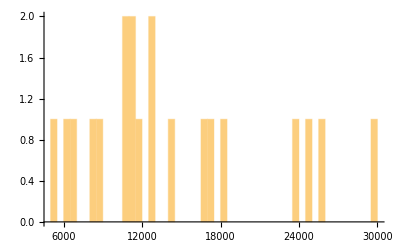

```mathematica
Histogram[Flatten@{polarfixationtime[[;;,2]],nematicfixationtime[[;;,2]]},50]
```

```mathematica
Manipulate[
l0=Line[{{localordertime[[i]],0},{localordertime[[i]],1}}];
l1=Line[{{fixationtimes[[i,2]],0},{fixationtimes[[i,2]],1}}];
l2=Line[{{boxfixationtimes[[i]],0},{boxfixationtimes[[i]],1}}];
ListPlot[{Thread[{timegrid2,polarorder[[i]]}],Thread[{timegrid2,nematicorder[[i]]}],Thread[{timegrid2,totfractpolorder[[i]]}],Thread[{timegrid2,totfractnemorder[[i]]}]},Joined->True,Epilog->{Directive[{Gray,Dashed}],l0,Directive[{Black,Dashed}],l1,Directive[{Gray,Thick,Dashing[None]}],l2}],{i,1,ensemblesize,1}]
```

```mathematica
{"local",Mean[localordertime]}
{"box",Mean[boxfixationtimes]}
{"polar",Mean[polarfixationtime[[;;,2]]]}
{"nematic",Mean[nematicfixationtime[[;;,2]]]}
{"total",Mean[fixationtimes[[;;,2]]]}
```

{local,280.777}

{box,4277.34}

{polar,15683.3}

{nematic,13296.}

{total,14370.3}

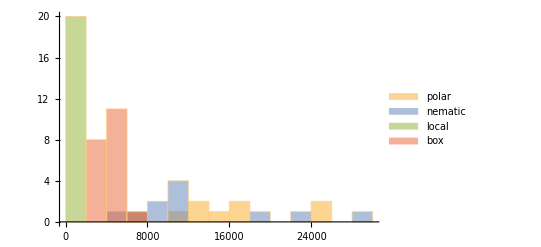

```mathematica
Histogram[{polarfixationtime[[;;,2]],nematicfixationtime[[;;,2]],localordertime,boxfixationtimes},20,PlotRange->All,ChartLegends->{"polar","nematic","local","box"}]
```

```mathematica
(*Export["localfixationtimes.mx",localordertime];
Export["boxfixationtimes.mx",boxfixationtimes];
Export["polarfixationtimes.mx",polarfixationtime[[;;,2]]];
Export["nematicfixationtimes.mx",nematicfixationtime[[;;,2]]];
Export["totalfixationtimes.mx",fixationtimes[[;;,2]]];*)
```

### Plotting single realizations

Note that time here is properly normalized

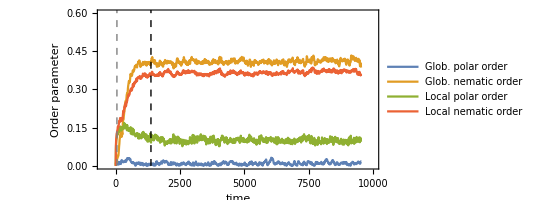

```mathematica
index=10;
timenorm=6.3;
l0=Line[{{localordertime[[index]]/timenorm,0},{localordertime[[index]]/timenorm,1}}];
l1=Line[{{fixationtimes[[index,2]]/timenorm,0},{fixationtimes[[index,2]]/timenorm,1}}];
l2=Line[{{boxfixationtimes[[index]]/timenorm,0},{boxfixationtimes[[index]]/timenorm,1}}];
plt=ListPlot[{Thread[{timegrid2/timenorm,polarorder[[index]]}],Thread[{timegrid2/timenorm,nematicorder[[index]]}],Thread[{timegrid2/timenorm,totfractpolorder[[index]]}],Thread[{timegrid2/timenorm,totfractnemorder[[index]]}]},Joined->True,Epilog->{Directive[{Gray,Dashed}],l0,Directive[{Black,Dashed}],l1(*,Directive[{Gray,Thick,Dashing[None]}],l2*)},Frame->True,PlotLegends->{Style["Glob. polar order",14],Style["Glob. nematic order",14],Style["Local polar order",14],Style["Local nematic order",14]},FrameLabel->{Style["time",14],Style["Order parameter",14]},PlotRange->{{-500,10000},{0,0.6}},AspectRatio->1/2]
```

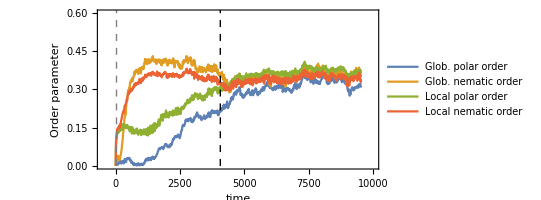

```mathematica
index=3;
timenorm=6.3;
l0=Line[{{localordertime[[index]]/timenorm,0},{localordertime[[index]]/timenorm,1}}];
l1=Line[{{fixationtimes[[index,2]]/timenorm,0},{fixationtimes[[index,2]]/timenorm,1}}];
l2=Line[{{boxfixationtimes[[index]]/timenorm,0},{boxfixationtimes[[index]]/timenorm,1}}];
plt=ListPlot[{Thread[{timegrid2/timenorm,polarorder[[index]]}],Thread[{timegrid2/timenorm,nematicorder[[index]]}],Thread[{timegrid2/timenorm,totfractpolorder[[index]]}],Thread[{timegrid2/timenorm,totfractnemorder[[index]]}]},Joined->True,Epilog->{Directive[{Gray,Dashed}],l0,Directive[{Black,Dashed}],l1(*,Directive[{Gray,Thick,Dashing[None]}],l2*)},Frame->True,PlotLegends->{Style["Glob. polar order",14],Style["Glob. nematic order",14],Style["Local polar order",14],Style["Local nematic order",14]},FrameLabel->{Style["time",14],Style["Order parameter",14]},PlotRange->{{-500,10000},{0,0.6}},AspectRatio->1/2]
```